# Making graphs for puro

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
myFile = Import["/Volumes/MINI 1/_PURO/NT TA TL puro counts.xlsx"];
```

```mathematica
myTimes = myFile[[3,1;;All,3]];
myTransSpots = myFile[[3,1;;All,2]];
```

```mathematica
myData = {myTimes,myTransSpots}//Transpose;
```

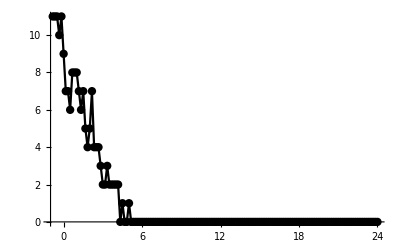

```mathematica
ListPlot[myData, PlotRange->All,Joined->True,AxesOrigin->{-1,0},PlotStyle->Black, Mesh->All]
```

```mathematica
Show[%334,PlotLabel->None,LabelStyle->{FontFamily->"Arial",24,GrayLevel[0]}]
```

-Graphics-

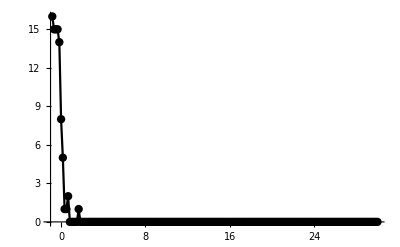

```mathematica
Show[%315,PlotLabel->None,LabelStyle->{FontFamily->"Arial",24,GrayLevel[0]}]
```

```mathematica
Show[%317,PlotLabel->None]
```

-Graphics-

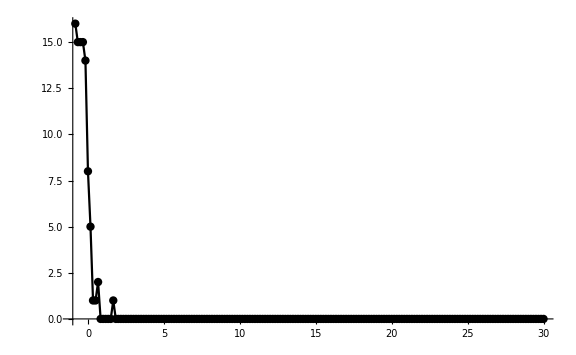

```mathematica
Show[%319,ImageSize->Large]
```

```mathematica
Show[%290,AxesLabel->{HoldForm[Time min],HoldForm[Number of translating RNA]},PlotLabel->None,LabelStyle->{FontFamily->"Arial",24,GrayLevel[0]}]
```

```mathematica
Show[%316,ImageSize->Large]
```

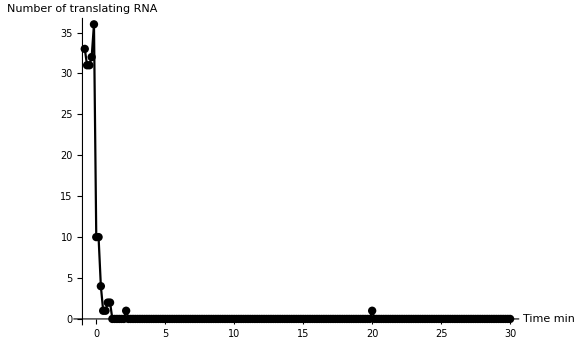

```mathematica
Show[%291,ImageSize->Large]
```

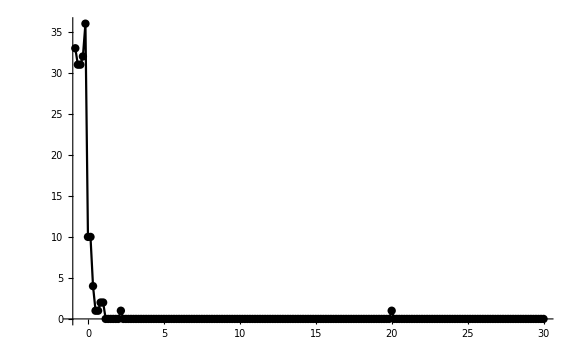

```mathematica
Show[%282,ImageSize->Large, FontSize-> 64]
```